```mathematica
Clear["Global`*"];
h=(R Cos[π/n])/Tan[φ];
Simplify[ArcCos[(R^2 Cos[(2π)/n]+h^2)/(R^2+h^2)]]
```

ArcCos[(Cos[(2 π)/n]+Cos[π/n]^2 Cot[φ]^2)/(1+Cos[π/n]^2 Cot[φ]^2)]

```mathematica
(*************************)
n=100;
φ=50°;
R=7;
(*************************)
h=(R Cos[π/n])/Tan[φ];
Show[

Table[
Graphics3D[{
RGBColor[0,1,1,1],
EdgeForm[],

Polygon[{
{R Cos[(i-1)(2π)/n],R Sin[(i-1)(2π)/n],0},
{R Cos[i(2π)/n],R Sin[i(2π)/n],0},
{0,0,-h}
}]
}],
{i,n}],

Boxed->False,
(*ViewPoint->20 {Cos[φ],Sin[φ],.3},
SphericalRegion->Sphere[{0,0,0},1],

PlotRange->{{,},{,},{,}},*)
Background->Black,
ImageSize->.2{1920,1080}
]
```

-Graphics3D-

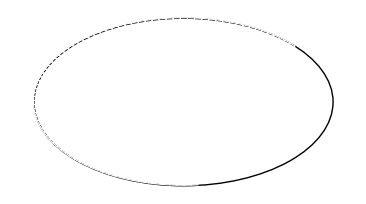

```mathematica
φmre=ArcCos[(Cos[(2 π)/n]+Cos[π/n]^2 Cot[φ]^2)/(1+Cos[π/n]^2 Cot[φ]^2)];
Rmre=√(R^2+h^2);
grafikamreže=Show[

Table[
Graphics[{
RGBColor[1,1,1,1],
EdgeForm[Thin],

Polygon[{
{Rmre Cos[(i-1)φmre],Rmre Sin[(i-1)φmre]},
{Rmre Cos[i φmre],Rmre Sin[i φmre]},
{0,0}
}]
}],
{i,n}],
Graphics[{
Circle[{0,0},Rmre],
EdgeForm[Thin]
}],

Boxed->False
]
```

```mathematica
Export[
StringJoin[{
"c:\\Users\\gal\\Downloads\\piramidni",
" n",ToString[n],
" R",ToString[R],
" φ",ToString[Round[N[φ/°]]],
".svg"
}],
grafikamreže];
CopyToClipboard[StringReplace[ToString[N[2Rmre]],"."->","]]
```